## Appendix A7 (Asymmetry in sensitivity to competition)

### Setup

```mathematica
f[a_,b_,v_,p_,q_]:= v NIntegrate[Exp[(-(x-p)^2)/a^2]Exp[(-(x-q)^4)/(81 b^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[(-(x-p)^2)/a^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]=Subscript[N, 1](1-S^4/Subscript[ω, 1]^4-(Subscript[α, 11] Subscript[N, 1]+Subscript[α, 12] Subscript[N, 2]))
Subscript[dN, 2]=Subscript[N, 2](1-(S-ϵ)^4/Subscript[ω, 2]^4-(Subscript[α, 21] Subscript[N, 1]+Subscript[α, 22] Subscript[N, 2]))
dS=Subscript[η, 1](-S)Subscript[N, 1]+Subscript[η, 2](ϵ-S)Subscript[N, 2];
```

N_1 (1-N_1 α_11-N_2 α_12-S^4/ω_1^4)

N_2 (1-N_1 α_21-N_2 α_22-(S-ϵ)^4/ω_2^4)

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

### Symmetric case for reference (same as Figure 2c)

#### Calculation

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,6,0.2];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
multiCoex=0;
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ11[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]];
λ12[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
λ1[[j1,j2]]=Min[λ11[[j1,j2]],λ12[[j1,j2]]];
If[λ11[[j1,j2]]<0&&λ12[[j1,j2]]<0,multiCoex++]];

If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{50.6094,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{0,1619,0,272,0,0}

```mathematica
multiCoex
```

0

#### Result

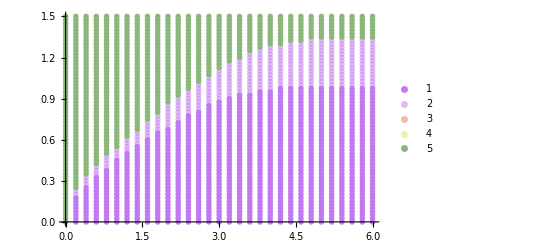

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

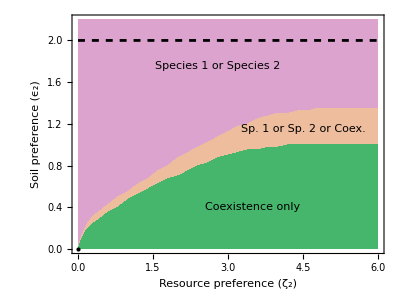

```mathematica
Show[{RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,2.2},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None],Plot[(Subscript[ω, 1]+Subscript[ω, 2])/.pars,{ζ,0,6},PlotStyle->{Dashed,Black}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{2.8,1.75}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex.",FontSize->13]],{4.5,1.15}],Inset[Text[Style["Coexistence only ",FontSize->13]],{3.5,0.4}]}},AspectRatio->0.75]
```

```mathematica
z1Sym=z1;
z2Sym=z2;
```

### Figure A6 (Asymmetry in ν)

#### Species 2 is better ν_1=1, ν_2=0.9

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->0.9,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ11=Array[,{nζ,nϵ}];
λ12=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ11[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]];
λ12[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
λ1[[j1,j2]]=Min[λ11[[j1,j2]],λ12[[j1,j2]]];
If[λ11[[j1,j2]]<0&&λ12[[j1,j2]]<0,multiCoex++]];

If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]>=0,y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{122.359,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{526,3751,28,331,0,0}

```mathematica
multiCoex
```

0

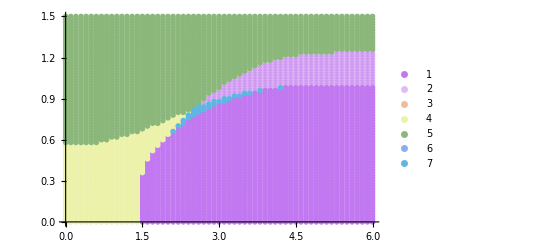

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
f3=Interpolation[z3];
```

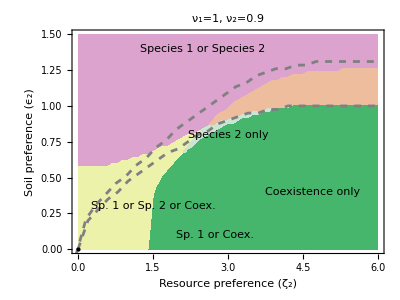

```mathematica
figA6a=Show[{RegionPlot[{y>f3[x]&&y>f1[x],f1[x]<y<f3[x],y<f2[x],f3[x]<y<f1[x],f2[x]<y<f1[x]&&y<f3[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.929162, 0.95034, 0.6648153333333333],RGBColor[0.7952328000000001, 0.8988539999999999, 0.8302508]},BoundaryStyle->None,MaxRecursion->5],ListLinePlot[{z1Sym,z2Sym-0.04},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["ν_1=1, ν_2=0.9",FontSize->20],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->18]],{2.5,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex.",FontSize->13]],{1.5,0.3}],Inset[Text[Style["Sp. 1 or Coex.",FontSize->13]],{2.75,0.1}],Inset[Text[Style["Species 2 only",FontSize->13]],{3,0.8}],Inset[Text[Style["Coexistence only ",FontSize->17]],{4.7,0.4}]}},AspectRatio->0.75]
```

```mathematica
z1d0=z1;
z2d0=z2;
z3d0=z3;
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA6a.jpg",figA6a];
```

#### Species 2 is worse ν_1=1, ν_2=1.1

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1.1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ11=Array[,{nζ,nϵ}];
λ12=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
y6=Array[,{nϵ*nζ,2}];
y7=Array[,{nϵ*nζ,2}];

eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Timing[
Do[
ch1=0;
ch2=0;
ch3=0;
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];

If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]]];

If[Length[eq[[j1,j2]]]==2,
λ11[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,1]]]]];
λ12[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
λ1[[j1,j2]]=Min[λ11[[j1,j2]],λ12[[j1,j2]]];
If[λ11[[j1,j2]]<0&&λ12[[j1,j2]]<0,multiCoex++]];

If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]]];

λ2[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1/Subscript[α, 11],Subscript[N, 2]->0,S->0}]]];

λ3[[j1,j2]]=Max[Re[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1/Subscript[α, 22],S->ϵs[[j2]]}]]];

eqCounts[[Min[Length[eq[[j1,j2]]],5]+1]]++;

If[λ1[[j1,j2]]<0&& (λ2[[j1,j2]]≥0||λ2[[j1,j2]]==Null[j1,j2])&& (λ3[[j1,j2]]≥0||λ3[[j1,j2]]==Null[j1,j2]),y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& (λ3[[j1,j2]]≥0||λ3[[j1,j2]]==Null[j1,j2]),y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&(λ2[[j1,j2]]≥0||λ2[[j1,j2]]==Null[j1,j2])&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& (λ3[[j1,j2]]≥0||λ3[[j1,j2]]==Null[j1,j2]),y6[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&&(λ2[[j1,j2]]≥0||λ2[[j1,j2]]==Null[j1,j2])&& λ3[[j1,j2]]<0,y7[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&ch3==0,z3[[j1]]={ζs[[j1]],ϵs[[j2]]};ch3=1],

{j2,nϵ}],
{j1,nζ}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{93.6875,Null}

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)
6 - coex + s1
7 - coex + s2

```mathematica
eqCounts
```

{488,3775,29,344,0,0}

```mathematica
multiCoex
```

0

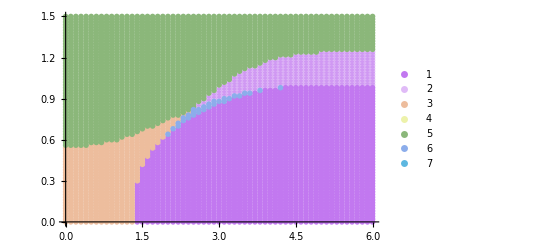

```mathematica
ListPlot[{y1,y2,y3,y4,y5,y6,y7},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]},ColorData[95,1],ColorData[95,6]}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
f3=Interpolation[z3];
```

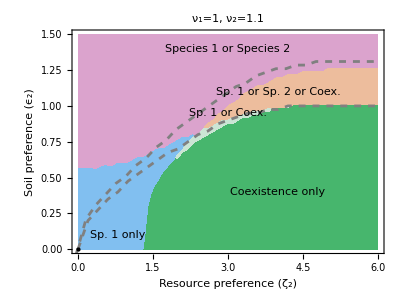

```mathematica
figA6b=Show[{RegionPlot[{y>f3[x],f2[x]<y<f3[x],y<f1[x],f3[x]<y<f2[x],f1[x]<y<f2[x]&&y<f3[x]},{x,0,6},{y,0,1.5},PlotStyle->{RGBColor[0.8570441666666667, 0.6373188333333333, 0.8020406666666666],RGBColor[0.927848, 0.742785, 0.6151383333333333],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[Rational[43, 85], Rational[191, 255], Rational[16, 17]],RGBColor[0.7952328000000001, 0.8988539999999999, 0.8302508]},BoundaryStyle->None,MaxRecursion->5],ListLinePlot[{z1Sym,z2Sym-0.04},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}]},PlotLabel->Style["ν_1=1, ν_2=1.1",FontSize->20],Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->18]],{3,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex.",FontSize->18]],{4,1.1}],Inset[Text[Style["Sp. 1 or Coex.",FontSize->15]],{3,0.95}],Inset[Text[Style["Sp. 1 only",FontSize->15]],{0.8,0.1}],Inset[Text[Style["Coexistence only ",FontSize->18]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
z1d2=z1;
z2d2=z2;
z3d2=z3;
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA6b.jpg",figA6b];
```

#### Summary

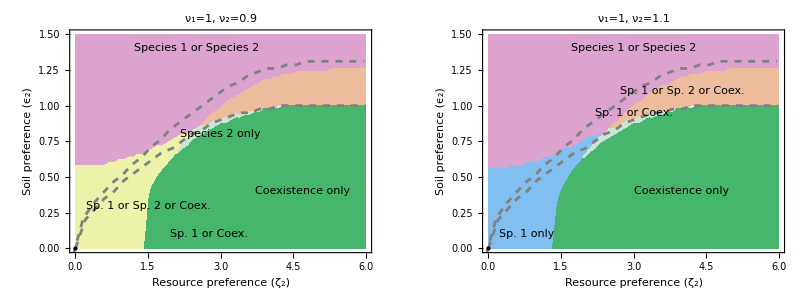

```mathematica
GraphicsRow[{figA6a,figA6b},ImageSize->800]
```

## Appendix A8 (Figure A12)

### Insensitive invader

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->0.9,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

```mathematica
Do[
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

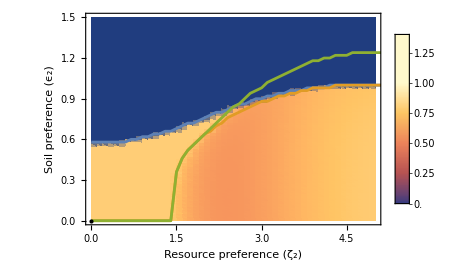

```mathematica
figA12a0=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.4}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.4}},ColorFunctionScaling->False],ListLinePlot[{z1d0,z2d0,z3d0}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

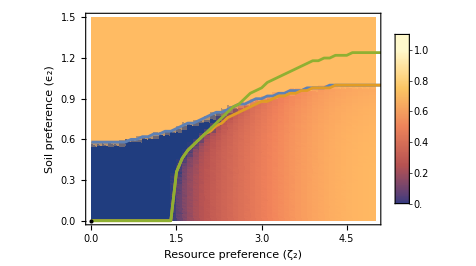

```mathematica
figA12b0=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1d0,z2d0,z3d0}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA12a0.jpg",figA12a0];
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA12b0.jpg",figA12b0];
```

### Sensitive invader

```mathematica
pars={Subscript[ω, 1]->1,Subscript[ω, 2]->1,Subscript[σ, 1]->1,Subscript[σ, 2]->1,Subscript[ν, 1]->1,Subscript[ν, 2]->1.1,Subscript[η, 1]->1,Subscript[η, 2]->1};
ϵs=Range[0,1.5,0.025];
nϵ=Length[ϵs];
ζs=Range[0,5,0.1];
nζ=Length[ζs];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nζ,3}];
yf=Array[,{nϵ*nζ,3}];
zf=Array[,{nϵ*nζ,3}];
```

```mathematica
x0=1;y0=0.001;z0=0; T=10000;
```

```mathematica
Do[
Do[
Subscript[α, 11]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,0];
Subscript[α, 12]=f[Subscript[σ, 1]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 1]/.pars,0,ζs[[j1]]];
Subscript[α, 21]=f[Subscript[σ, 2]/.pars,Subscript[σ, 1]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],0];
Subscript[α, 22]=f[Subscript[σ, 2]/.pars,Subscript[σ, 2]/.pars,Subscript[ν, 2]/.pars,ζs[[j1]],ζs[[j1]]];
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{ζs[[j1]],ϵs[[j2]],z[T]/.nsol}],
{j2,nϵ}],
{j1,nζ}]
```

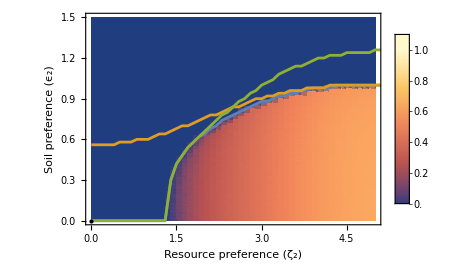

```mathematica
figA12a1=Show[{ListDensityPlot[yf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1d2,z2d2,z3d2}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

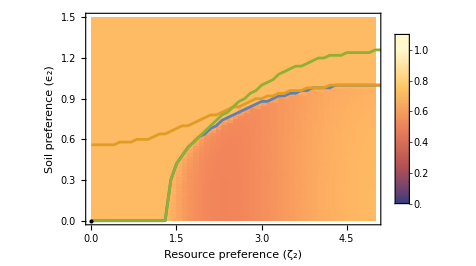

```mathematica
figA12b1=Show[{ListDensityPlot[xf,PlotLegends->BarLegend[{Automatic,{-0.001,1.1}}],PlotRange->{{0,5},{0,1.5},{-0.001,1.1}},ColorFunctionScaling->False],ListLinePlot[{z1d2,z2d2,z3d2}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {PointSize[Large],Point[{0,0}]},AspectRatio->2/3]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA12a1.pdf",figA12a1];
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figA12b1.pdf",figA12b1];
```